Swapped Hexagons: {8,7}

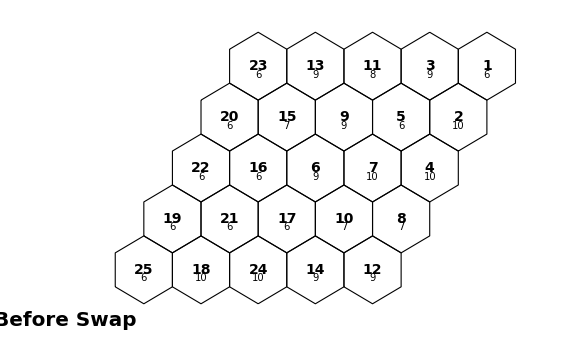
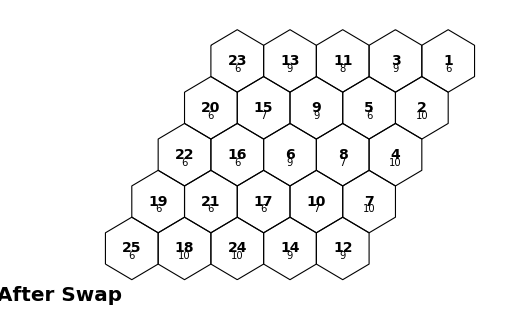

```mathematica
swapAmphiphiles[gridSize_]:=Module[
	  {hexGrid,vertexCoords,hexagonCycles,randomIntegers,adjacentHexagonsList,swappedHexagons},
	  
	  (* Create hexagonal grid graph *)
	  hexGrid=[gridSize];
	  
	  (* Get vertex coordinates *)
	  vertexCoords=GraphEmbedding[hexGrid];
	  
	  (* Identify hexagonal cycles *)
	  hexagonCycles=FindCycle[hexGrid,{6},All];
	  
	  (* Generate random integers for each hexagon *)
	  randomIntegers=RandomInteger[{6,10},Length[hexagonCycles]];
	  
	  (* Function to plot hexagons with labels *)
	  plotHexagons[cycles_,vertexCoords_,randomIntegers_,plotLabel_]:=Module[{hexagonLabels},
	    hexagonLabels=Table[
	      {
	        Text[Style[i,Bold,14],Mean[vertexCoords[[cycles[[i,All,1]]]]]],
	        Text[Style[randomIntegers[[i]],Italic,10],
	          Mean[vertexCoords[[cycles[[i,All,1]]]]]-{0,0.5}]
	      },
	      {i,Length[cycles]}
	    ];
	    Graphics[{Text[Style[plotLabel,Bold,20],{-3,-2}],EdgeForm[Black],FaceForm[],
	      Polygon[vertexCoords[[#]]] & /@ (cycles[[All,All,1]]),hexagonLabels}]
	  ];
	  
	  (* Plot hexagons before swap *)
	  plotBefore=plotHexagons[hexagonCycles,vertexCoords,randomIntegers,"Before Swap"];
	  
	  (* Function to find adjacent hexagons for a given hexagon *)
	  findAdjacentHexagons[hexagonIndex_]:=Module[{hexagonVertices,adjacentHexagons},
	    hexagonVertices=hexagonCycles[[hexagonIndex,All,1]];
	    adjacentHexagons=Select[Range[Length[hexagonCycles]],
	      Intersection[hexagonCycles[[#,All,1]],hexagonVertices]=!={}&&#!=hexagonIndex &];
	    adjacentHexagons
	  ];
	  
	  (* List of adjacent hexagons for each hexagon *)
	  adjacentHexagonsList=findAdjacentHexagons /@ Range[Length[hexagonCycles]];
	  
	  (* Function to swap two hexagons and return swapped indices *)
	  swapHexagons[hexagonIndex_]:=Module[{adjacent,swapIndex},
	    adjacent=adjacentHexagonsList[[hexagonIndex]];
	    If[Length[adjacent]>0,
	      swapIndex=RandomChoice[adjacent];
	      (* Swap the positions of hexagonIndex and swapIndex in hexagonCycles *)
	      hexagonCycles[[{hexagonIndex,swapIndex}]]=hexagonCycles[[{swapIndex,hexagonIndex}]];
	      (* Return the indices of the swapped hexagons *)
	      {hexagonIndex,swapIndex},
	      "No adjacent hexagons to swap"
	    ]
	  ];
	  
	  (* Randomly select a hexagon and swap it with an adjacent hexagon *)
	  swappedHexagons=swapHexagons[RandomInteger[{1,Length[hexagonCycles]}]];
	  
	  (* Print the indices of the swapped hexagons *)
	  Print["Swapped Hexagons: ",swappedHexagons];
	  
	  (* Plot hexagons after swap *)
	  plotAfter=plotHexagons[hexagonCycles,vertexCoords,randomIntegers,"After Swap"];
	  
	  (* Display plots before and after swap *)
	  {plotBefore,plotAfter}
	]
	
	(* Example usage *)
	swapAmphiphiles[{5,5}]
```